# Introdução à Física Computacional I (2022.2)

## Aula 12: fractais; o triângulo de Sierpinski; o conjunto de Mandelbrot

## Fractais

Como já mencionamos em outras aulas, fractais são figuras em que o mesmo padrão ocorre em diferentes escalas, descendo até o infinitesimalmente pequeno. Na Natureza, diversos padrões são aproximadamente fractais, como as costas dos continentes, flocos de neve e a estrutura ramificada dos vegetais e do sistema circulatório animal. Aqui vamos estudar fractais matemáticos “exatos”.

## O triângulo de Sierpinski

No Mathematica, aproximantes de fractais podem ser construídos com o auxílio de recursões. Como exemplo, vamos construir o fractal conhecido como “triângulo de Sierpinski”, cujo elemento básico é um triângulo equilátero.

Começamos criando uma lista que armazena coordenadas os vértices de um triângulo equilátero de lado unitário:

```mathematica
trianguloinicial={{0.,0.},{0.5,Sqrt[3./4.]},{1.,0.}};
```

Podemos visualizar o triângulo com a ajuda da primitiva Polygon para a função Graphics:

```mathematica
(*A função graphics desenha objetos geometricos*)
```

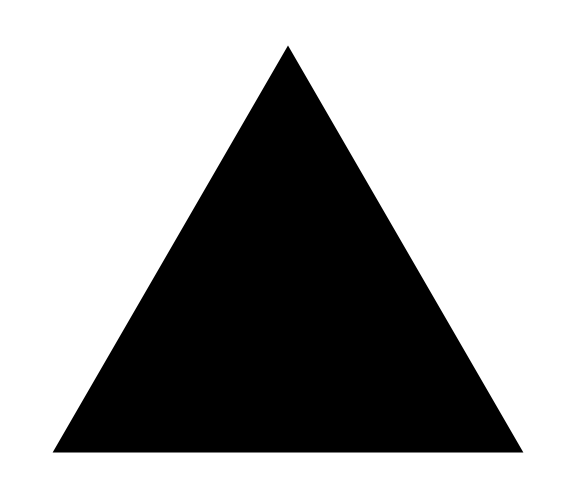

```mathematica
optam={ImageSize-> Large,LabelStyle-> {"Large"}};   
Show[Graphics[Polygon[trianguloinicial]],Evaluate[optam]]
```

```mathematica
(*Existem duas formas de construir o fractal desse triangulo: método da inflação e da erupção. Na erupção a gente desenha novos triangulos com base nos pontos medios dos lados do triangulo inicial e retira o triangulo central criado. Na inflação o processo é "oposto". Novos triangulos vao sendo somados para construir a figura principal.*)
```

Agora vamos criar uma função que, a partir de um triângulo definido pela lista t, cria uma tripla de triângulos t_1, t_2 e t_3 a partir dos vértices e do ponto médio dos lados de t:

```mathematica
(*A função "Module" é utilizada para definir variaveis locais (que nao serao utilizadas em blocos posteriores de codigo).*)
```

```mathematica
triplica[t_]:=Module[{t1,t2,t3},
t1={t[[1]],0.5*(t[[1]]+t[[2]]),0.5*(t[[1]]+t[[3]])};
t2={t[[2]],0.5*(t[[2]]+t[[3]]),0.5*(t[[2]]+t[[1]])};
t3={t[[3]],0.5*(t[[3]]+t[[1]]),0.5*(t[[3]]+t[[2]])};
{t1,t2,t3}
]
```

Aplicar a função triplica à lista trianguloinicial produz uma lista de três listas, cada uma contendo as coordenadas dos vértices dos novos triângulos:

```mathematica
triplica[trianguloinicial]
```

{{{0.,0.},{0.25,0.433013},{0.5,0.}},{{0.5,0.866025},{0.75,0.433013},{0.25,0.433013}},{{1.,0.},{0.5,0.},{0.75,0.433013}}}

A primitiva Polygon recebe como argumento básico uma lista de pontos que define um só polígono, mas podemos invocá-la usando como argumento uma lista de polígonos para produzir um polígono com buracos:

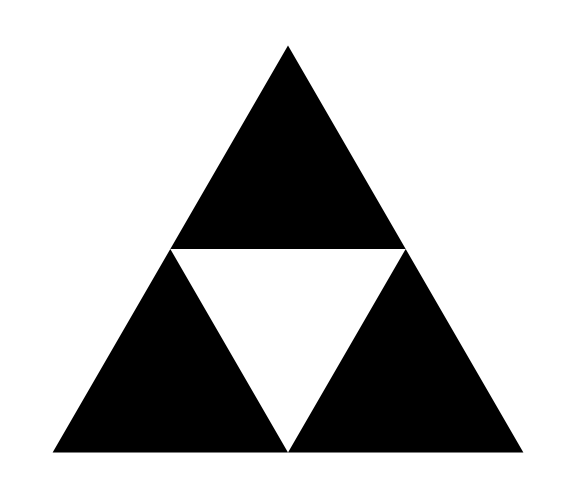

```mathematica
Show[Graphics[Polygon[triplica[trianguloinicial]]],Evaluate[optam]]
```

No entanto, as linhas do gráfico ficam mais suaves se utilizamos a função Map para aplicar Polygon separadamente a cada triângulo na tripla:

```mathematica
Show[Graphics[Map[Polygon,triplica[trianguloinicial]]],Evaluate[optam]]
```

-Graphics-

No restante da aula, vamos utilizar a notação compacta Polygon/@lista para representar Map[Polygon,lista]:

```mathematica
Show[Graphics[Polygon/@triplica[trianguloinicial]],Evaluate[optam]]
```

-Graphics-

Cada triângulo nessa figura tem lados iguais a 1/2. Note, no entanto, que o comprimento total das bordas internas e externas do conjunto é 3×3×1/2=3×(3/2) daquele do triângulo original, enquanto a área sombreada corresponde a apenas 3/4 da área do triângulo original. 
(*O comprimento total dos lados desse objeto aumenta, mas a area sombreada diminui*)

Temos agora os elementos básicos para iterar o processo um número arbitrário de vezes, construindo uma lista de triângulos de tamanhos variados, começando de um único triângulo:

```mathematica
listainicial={trianguloinicial}
```

{{{0.,0.},{0.5,0.866025},{1.,0.}}}

Embora isso não seja necessário nesta etapa, vamos “mapear” listainicial com a função triplica para produzir a primeira iteração:

```mathematica
lista2=Flatten[triplica/@listainicial,1]
```

{{{0.,0.},{0.25,0.433013},{0.5,0.}},{{0.5,0.866025},{0.75,0.433013},{0.25,0.433013}},{{1.,0.},{0.5,0.},{0.75,0.433013}}}

Note o uso de Flatten para remover uma camada de chaves e fazer de lista2 uma lista de triângulos, assim como era listainicial.

Estamos agora na mesma etapa do último gráfico mostrado. Vamos repetir o procedimento, substituindo listainicial por lista2, para criar a próxima iteração:

```mathematica
lista3=Flatten[triplica/@lista2,1]
```

{{{0.,0.},{0.125,0.216506},{0.25,0.}},{{0.25,0.433013},{0.375,0.216506},{0.125,0.216506}},{{0.5,0.},{0.25,0.},{0.375,0.216506}},{{0.5,0.866025},{0.625,0.649519},{0.375,0.649519}},{{0.75,0.433013},{0.5,0.433013},{0.625,0.649519}},{{0.25,0.433013},{0.375,0.649519},{0.5,0.433013}},{{1.,0.},{0.75,0.},{0.875,0.216506}},{{0.5,0.},{0.625,0.216506},{0.75,0.}},{{0.75,0.433013},{0.875,0.216506},{0.625,0.216506}}}

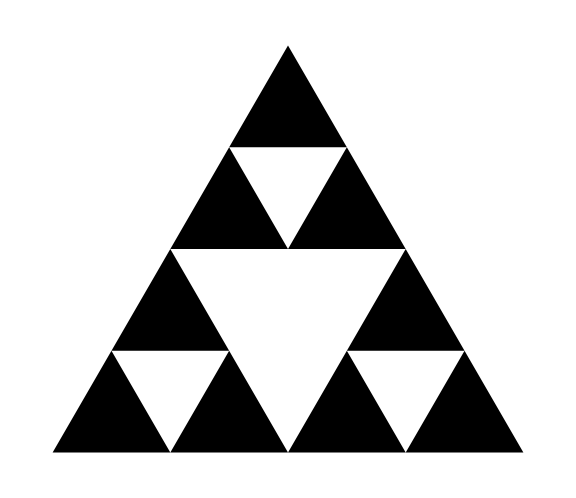

```mathematica
Show[Graphics[Polygon/@lista3],Evaluate[optam]]
```

Agora cada triângulo nessa figura tem lados iguais a (1/2)^2. O comprimento total é igual a 3^2×3×(1/2)^2=3×(3/2)^2, enquanto a área sombreada corresponde a (3/4)^2 da área do triângulo original.

Para automatizar o processo de iteração, vamos definir uma função itera que recebe como argumento uma lista de triângulos e a triplica. Em seguida, podemos utilizar Nest para repetir o processo quantas vezes desejarmos, começando do triângulo inicial:

```mathematica
itera[lista_]:=Flatten[triplica/@lista,1]
listafinal[n_]:=Nest[itera,listainicial,n]
```

Agora podemos produzir diversas aproximações sucessivas do triângulo de Sierpinski:

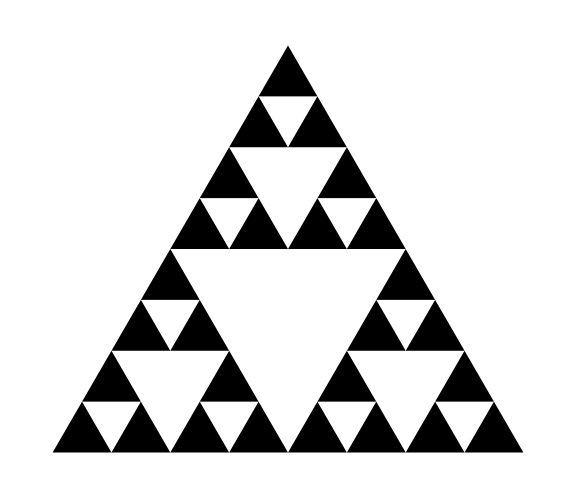

```mathematica
Show[Graphics[Polygon/@listafinal[3]],Evaluate[optam]]
```

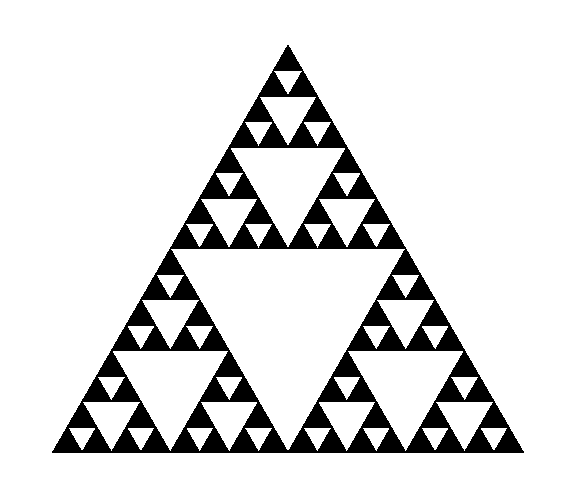

```mathematica
Show[Graphics[Polygon/@listafinal[4]],Evaluate[optam]]
```

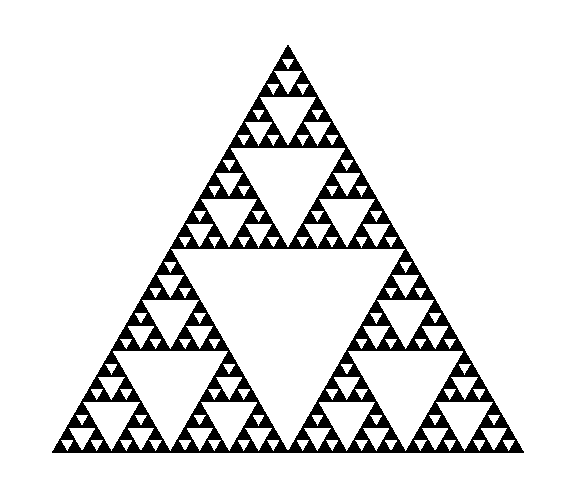

```mathematica
Show[Graphics[Polygon/@listafinal[5]],Evaluate[optam]]
```

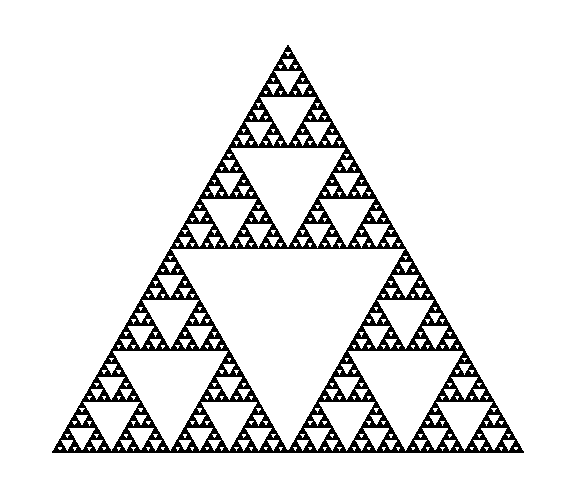

```mathematica
Show[Graphics[Polygon/@listafinal[6]],Evaluate[optam]]
```

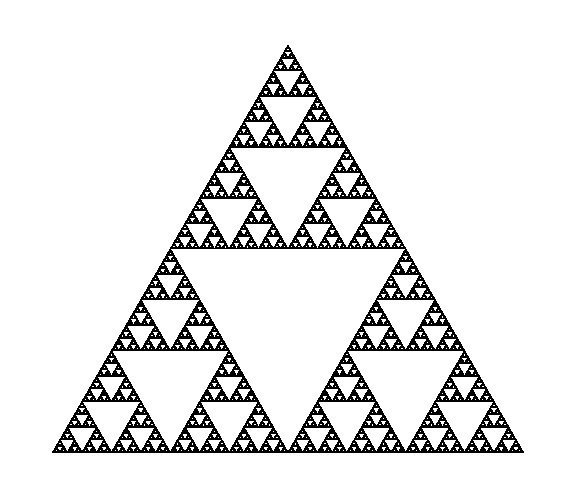

```mathematica
Show[Graphics[Polygon/@listafinal[7]],Evaluate[optam]]
```

Se nos concentrarmos na metade superior da figura após n iterações, observamos, no limite n→∞, uma cópia reescalada da figura original. Essa invariância de escala é o que define os fractais.

Após n iterações, temos 3^n triângulos, cada um com lado igual a (1/2)^n, produzindo um comprimento total 3×(3/2)^n e uma área total (3/4)^n da área do triângulo original. Vemos assim que, no limite n→∞, o perímetro externo se mantém igual a 3, enquanto o comprimento total diverge e a área tende a zero!

Construímos o fractal pelo processo de redução de escala. Mas poderíamos ter percorrido o caminho inverso, partindo de um triângulo de lado unitário e arranjando cópias do triângulo no mesmo padrão do triângulo de Sierpinski. Se fizermos isso, após n iterações teremos 3^n triângulos, cada um com perímetro igual a 3, formando uma figura em que

as arestas externas têm lado L=2^n;

a área total A é 3^n vezes a área do triângulo original, o que é proporcional a 3^(ln(L)/ln(2))=L^(ln(3)/ln(2)).

Mas há algo bem estranho nesse processo, quando comparamos com um processo semelhante envolvendo um padrão “sólido”, ou seja, sem espaços vazios no interior. Partindo de um triângulo de lado unitário, para produzir um triângulo sólido com lado igual a 2 teríamos que usar 4 triângulos, resultando em um perímetro externo igual a 3×2 e em uma área total igual a 4 vezes a área do triângulo original. Após n iterações do processo, teríamos um triângulo sólido com lado L=2^n construído a partir de 4^n triângulos, resultando em um perímetro externo 3×2^n e em uma área total 4^n vezes a área do triângulo original. A razão entre o perímetro externo e a área total é proporcional 2^n/4^n=(1/2)^n, e portanto vai a zero quando n→∞. Além disso, a área total A é proporcional a 4^(ln(L)/ln(2))=L^(ln(4)/ln(2))=L^2, como esperado para um objeto bidimensional.

A discussão acima motiva a introdução de uma dimensão fractal d_f, também chamada de dimensão de Hausdorff. No caso de um objeto definido em um espaço bidimensional, d_f é o expoente que dá a relação entre a área A e o comprimento característico L do objeto, A∝L^d_f. Para o triângulo de Sierpinski, como mostramos acima, essa dimensão é d_f=ln(3)/ln(2)≃1.58. Para objetos tradicionais, a dimensão fractal coincide com a dimensão espacial, como no caso do triângulo sólido.

## O conjunto de Mandelbrot

O conjunto de Mandelbrot é um fractal definido como o conjunto de todos os pontos (c_x,c_y) no plano complexo tais que o mapa
z_(n+1)=z_n^2+c,
com c=c_x+i c_y, não tende ao infinito a partir de z=0. 
O Mathematica dispõe de uma função intrínseca para produzir o conjunto de Mandelbrot (veja aqui), mas será mais instrutivo para nós se escrevermos nossa própria função.

Para isso, teríamos que testar se o mapa escapa para o infinito com cada valor de c que escolhermos. Isso é impossível em um computador, mas existe um resultado matemático que garante que tende ao infinito um mapa que produz um valor de z_n tal que |z_n|>2. Além desse teste, temos que impor um número máximo de aplicações do mapa, após o qual consideramos que o valor correspondente de c pertence ao conjunto de Mandelbrot. Eis uma função compilada que implementa esses testes, fazendo uso de um novo tipo de laço, While, que envolve um condicional:

```mathematica
mandelbrot:=Compile[{cx,cy,nmax},
Module[{z=0.+I*0.,n=0}, (* z é "declarado" como complexo *)
(
While[Abs[z]≤2 && n≤nmax, 
(
z=z^2+cx+I*cy;
n++
)
];
n
)
]
]
```

Note a sintaxe da função While: o primeiro argumento é a condição (nesse caso, a combinação de duas condições simultâneas) e o segundo argumento contém as instruções a serem executadas. A última instrução, n++, é uma notação compacta para n=n+1, também utilizada em linguagens de programação como C e Python. A função retorna o número de repetições do laço, e os pontos que consideramos pertencerem ao conjunto são rotulados por nmax. (Todos os parênteses na função mandelbrot poderiam ter sido omitidos, mas optamos por incluí-los por clareza.)

Vamos testar a função com c=1+i:

```mathematica
mandelbrot[1,1,50]
```

2

O laço é executado duas vezes: na primeira vez, com z_0=0, temos z_1=z_0^2+c=0+1+i=1+i, com |z_1|=√2<2. Da segunda vez, temos z_2=z_1^2+c=(1+i)^2+1+i=1+3i, com |z_2|=√10>2, e o laço é interrompido.

Para visualizar o conjunto de Mandelbrot, vamos introduzir uma modalidade nova de gráficos, os gráficos de densidade. Trata-se de um tipo de gráfico tridimensional, ou seja, de funções de duas variáveis, projetado no plano das variáveis segundo um código de cores que representa o valor da função em cada ponto do plano. Para produzir esse gráfico, utilizamos a função DensityPlot, cuja sintaxe é a seguinte:

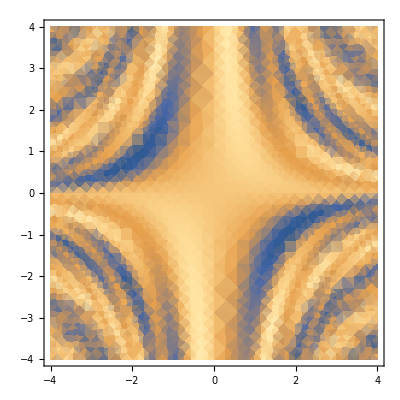

```mathematica
DensityPlot[Sin[x y]+Cos[x^2 y],{x,-4,4},{y,-4,4}]
```

```mathematica
DensityPlot[mandelbrot[x,y,200],{x,-2,0.6},{y,-1.3,1.3},PlotPoints->200,Evaluate[optam],PlotLegends->Automatic]
```

-Graphics-

Note que especificamos intervalos para ambos os eixos do gráfico. A opção PlotLegends→Automatic produz uma escala para as cores utilizadas. A figura tem um formato que lembra um coração, e é às vezes chamada de “cardioide”. A visualização fica mais atraente se utilizarmos a opção ScalingFunctions para colorir os pontos em escala logarítmica.

```mathematica
DensityPlot[mandelbrot[x,y,200], {x,-2,0.6},{y,-1.3,1.3},ScalingFunctions-> "Log",PlotPoints->200,Evaluate[optam],PlotLegends->Automatic]
```

-Graphics-

Se agora ampliarmos a região nas vizinhanças de c=0.8i, observamos claramente a estrutura fractal:

```mathematica
DensityPlot[mandelbrot[x,y,200], {x,-0.3,0.1},{y,0.6,1.0},ScalingFunctions-> "Log",PlotPoints->200,Evaluate[optam],PlotLegends->Automatic]
```

-Graphics-

Vamos ampliar ainda mais, tomando o cuidado de permitir mais aplicações do mapa, de modo a revelar melhor os detalhes na borda do conjunto:

```mathematica
DensityPlot[mandelbrot[x,y,1000], {x,-0.75,-0.747},{y,0.06,0.063},ScalingFunctions-> "Log",PlotPoints->200,ImageSize->Large,PlotLegends->Automatic]
```

-Graphics-

Existe uma rica estrutura no conjunto, inclusive nas espirais que aparecem na última figura. Com paciência, é possível explorá-la! Para os impacientes, a página da Wikipedia sobre o conjunto mostra muitos detalhes.

Como último tópico, vamos mencionar a relação entre o conjunto de Mandelbrot e o mapa logístico. Se c for um número real, partindo de z=0 o mapa de Mandelbrot produz apenas números reais. Fazendo a transformação z_n=-4λ x_n+2λ e substituindo no mapa de Mandelbrot, temos
-4λ x_(n+1)+2λ=(-4λ x_n+2λ)^2+c=4 λ^2-16 λ^2 x_n+16 λ^2 x_n^2+c.
Se escolhermos c=2λ (1-2λ), a equação anterior pode ser simplificada para
x_(n+1)=4λ x_n (1-x_n), 
exatamente a equação do mapa logístico. Quando λ varia no intervalo (1/4,1), em que o mapa logístico tem atratores diferentes de x=0, c varia no intervalo de 1/4 a -2. Os pontos c em que a fronteira do conjunto de Mandelbrot toca o eixo real correspondem aos valores de λ em que ocorrem as bifurcações do mapa logístico, como mostra a figura abaixo:

-Graphics-

## Exercícios

Façam os exercícios relativos à aula de hoje. A entrega pode ser feita até as 23h55 do dia 5 de dezembro.